```mathematica
explicitSum[f_,stepsize_,d_]:=stepsize^d Sum[f@@(x/@Range[d]),##]&@@Sequence[Table[{x[i],0,1,stepsize},{i,1,d}]]

totalSum[f_,stepsize_,d_]:=stepsize^d findSum[f,stepsize,d]
```

```mathematica
coeffs=fullCoefficients[Sin[Pi #[[1]]+#[[2]]]&,{3,3}];
```

```mathematica
Sqrt[0.005^2 Sum[(Sin[Pi i+j]-fullReconstruct[coeffs,{i,j}])^2,{i,0,1,.005},{j,0,1,.005}]]
```

0.0107815

```mathematica
Timing[Sqrt[0.005^2 Sum[(Sin[Pi i+j]-fullReconstruct[coeffs,{i,j}])^2,{i,0,1,.005},{j,0,1,.005}]]]
```

{171.407,0.0107815}

```mathematica
Table[Sqrt[0.05^2 Sum[(Sin[Pi i+j]-fullReconstruct[#,{i,j}])^2,{i,0,1,.05},{j,0,1,.05}]&@fullCoefficients[Sin[Pi #[[1]]+#[[2]]]&,{n,n}]],{n,1,5}]
```

```mathematica
fullError={0.16428309358579668,0.04311824666968759,0.010922142274398607,0.0027395147070991195,0.0006854411527070881}
```

{0.164283,0.0431182,0.0109221,0.00273951,0.000685441}

```mathematica
sparseError=Table[Sqrt[0.05^2 Sum[(Sin[Pi i+j]-fullReconstruct[#,{i,j}])^2,{i,0,1,.05},{j,0,1,.05}]&@sparseCoefficients[Sin[Pi #[[1]]+#[[2]]]&,n,2]],{n,1,7}]
```

{0.15943,0.106909,0.0340714,0.0106635,0.00322183,0.000956049,0.00027648}

```mathematica
fullLengths=Table[fullCoefficients[Sin[Pi #[[1]]+#[[2]]]&,{n,n}]//Length,{n,1,5}]
```

{9,25,81,289,1089}

```mathematica
sparseLengths=Table[sparseCoefficients[Sin[Pi #[[1]]+#[[2]]]&,n,2]//Length,{n,1,7}]
```

{6,12,25,53,113,241,513}

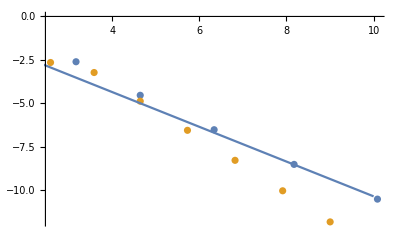

```mathematica
Show[ListPlot[{Table[{fullLengths[[i]],fullError[[i]]},{i,1,Length[fullError]}],Table[{sparseLengths[[i]],sparseError[[i]]},{i,1,Length[sparseError]}]}//Log2],Plot[-1 x-.35,{x,0,10}]]
```

```mathematica
Table[Sqrt[0.05^3 Sum[(Sin[Pi i+j+Pi k]-fullReconstruct[#,{i,j,k}])^2,{i,0,1,.05},{j,0,1,.05},{k,0,1,.05}]&@sparseCoefficients[Sin[Pi #[[1]]+#[[2]]+Pi#[[3]]]&,n,3]],{n,1,3}]
```

{1.15677,0.291658,0.360107}

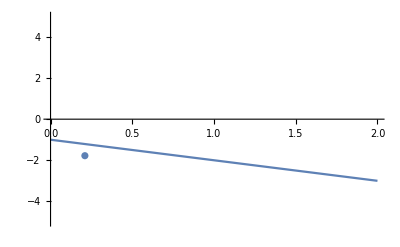

```mathematica
Show[Plot[-x-1,{x,0,2},PlotRange->5],ListPlot[{{0.27401112370472946,0.07750475000539797},{1.1567707982179598,0.29165751883293595}}//Log2]]
```

```mathematica
NIntegrate[(Sin[Pi x+y]-fullReconstruct[#,{i,j}])^2,{x,0,1},{y,0,1}]&@spCoefficients[Sin[Pi #[[1]]+#[[2]]]&]
```

```mathematica
{1.1567707982179598,0.29165751883293595}//Log2
```

{0.210103,-1.77765}

```mathematica
upperBound[x_,stepsize_]:=stepsize Floor[x/stepsize]
lowerBound[x_,stepsize_]:=stepsize Ceiling[x/stepsize]

construct[coeffs_,x_,n_]:=Module[{indices},indices=pointIndex[x,{n,n}];
Return[Sum[coeffs[[k1+2,indices[[1,k1+2]],k2+2,indices[[2,k2+2]]]] ϕ[{k1,k2},{indices[[1,k1+2]],indices[[2,k2+2]]}][#],{k1,-1,n},{k2,-1,n}]&
];

]

getSquare[f_,coeffs_,n_,X1_,X2_,stepsize_]:=Module[{g},g=construct[coeffs,{(X1+1/2)/2^(n-1),(X2+1/2)/2^(n-1)},n];(*Construct a function only for this square we care about*)

Return[
Sum[(f[{i,j}]-g[{i,j}])^2,(*Calculate the actual error here*)
{i,lowerBound[X1/2^(n-1),stepsize],(X1+1)/2^(n-1),stepsize},{j,lowerBound[X2/2^(n-1),stepsize],(X2+1)/2^(n-1),stepsize}]
(*Go from an appropriately shifted lowerbound to account for the different stepsize discretization*)
];
]

getError2D[f_,n_,stepsize_]:=Module[{coeffs},coeffs=fullCoefficients[f,{n,n}];Return[Sqrt[Sum[getSquare[f,coeffs,n,X1,X2,stepsize],{X1,0,2^(n-1)-1},{X2,0,2^(n-1)-1}]]];]

(*OMG THERES A MUCH MORE EFFICIENT O(P1 + P2) WAY*)
```

```mathematica
getError2D[Sin[Pi #[[1]]+#[[2]]]&,4,.01]//Timing
```

{13.8684,0.274457}

```mathematica
naiveError2D[f_,n_,stepsize_]:=Module[{coeffs,g,sum},coeffs=fullCoefficients[f,{n,n}];
g=fullReconstruct[coeffs,#,{n,n}]&;sum=Sum[(f[{i,j}]-g[{i,j}])^2,{i,0,1,stepsize},{j,0,1,stepsize}];
Return[sum];]

(*Working*)
```

```mathematica
naiveError2D[Sin[Pi #[[1]]+#[[2]]]&,4,.01]//Timing
```

{20.548,0.07345}

```mathematica
coeffs=fullCoefficients[Sin[Pi #[[1]]+#[[2]]]&,{4,4}];
Sum[(#[{x,y}]-Sin[Pi x+y])^2,{x,.5,.625,.01},{y,.5,.625,.01}]&@construct[coeffs,{.6,.6},4]
```

```mathematica
pointIndex[{.6,.6},{4,4}]
```

{{1,1,1,2,3,5},{1,1,1,2,3,5}}

```mathematica
lowerBound[.54,.01]
upperBound[.5+1/8,.01]
```

0.54

0.62

```mathematica
neighborAverage1D[f_,x_List,n_]:=Module[{below,above},below=2^-n Floor[x[[1]] 2^n];above=2^-n Ceiling[x[[1]] 2^n]; If[above==below,Return[f[{above}]];,Return[(above-x[[1]])/(above-below)f[{below}]+(x[[1]]-below)/(above-below)f[{above}]];]]

neighborAverage[f_,x_,n_]:=Module[{above,below},If[Length[x]==1,Return[neighborAverage1D[f,x,n]];,
Return[neighborAverage1D[Function[q,neighborAverage[Function[p,f[Join[q,p]]],x[[2;;]],n]],{x[[1]]},n]
] (*A little convoluted, but still good*)
]
]
```

```mathematica
Plot3D[neighborAverage[Sin[Pi #[[1]]+#[[2]]]&,{x,y},3]-fullReconstruct[#,{x,y},{3,3}],{x,0,1},{y,0,1}]&@fullCoefficients[Sin[Pi #[[1]]+#[[2]]]&,{3,3}] (*Good*)
```

-Graphics3D-

```mathematica
neighborError2D[f_,n_,stepsize_]:=Module[{ans},ans=Sqrt[stepsize^2 Sum[(f[{i,j}]-neighborAverage[f,{i,j},n])^2,{i,0,1,stepsize},{j,0,1,stepsize}]]; Return[ans]]

sparseNeighborError2D[f_,n_,stepsize_]:=Module[{values,ans},
For[i=0,i≤1,+=2^(-n□)
ans=Sqrt[stepsize^2 Sum[(f[{i,j}]-neighborAverage[values,{i,j},n])^2,{i,0,1,stepsize},{j,0,1,stepsize}]]; Return[ans]]
```

```mathematica
timesAndErrors=Table[neighborError[Sin[Pi #[[1]]+#[[2]]]&,n,.005]//Timing,{n,1,9}]
```

{{5.95466,0.161315},{5.98509,0.0425578},{6.20322,0.0107815},{6.40998,0.00270442},{6.38075,0.000676673},{6.46115,0.000169204},{6.47126,0.0000423032},{6.5194,0.0000105759},{6.49123,2.64399×10^-6}}

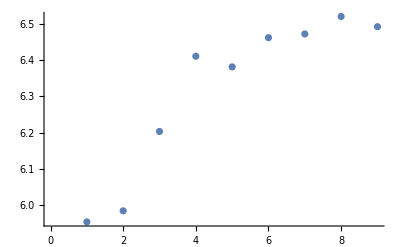

```mathematica
ListPlot[timesAndErrors[[;;,1]]]
```

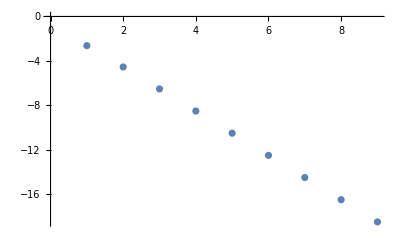

```mathematica
ListPlot[timesAndErrors[[;;,2]]//Log2]
```

```mathematica
neighborAverage[Sin[Pi #[[1]]+#[[2]]]&,{.3,.4},5]//Timing//ScientificForm
```

{3.07×10^-4,9.72848×10^-1}

```mathematica
f[0]=1
```

1